```mathematica
e
```

```mathematica
numeraiData=Import["/home/tamellan/Desktop/Numerai/numerai_training_data.csv"];
```

Ideas -- 
1) Train net based on 10 most output correlated features.
2) Train net based on 10 most output correlated features with maximal orthogonality - compressive sensing.
3) Fourier transform to extract a periodicity.
4) Check L1 reg and decision trees in Mathematica 11.2.

```mathematica
numeraiData//Dimensions
```

{535714,54}

```mathematica
Last[{535714,54}]
```

54

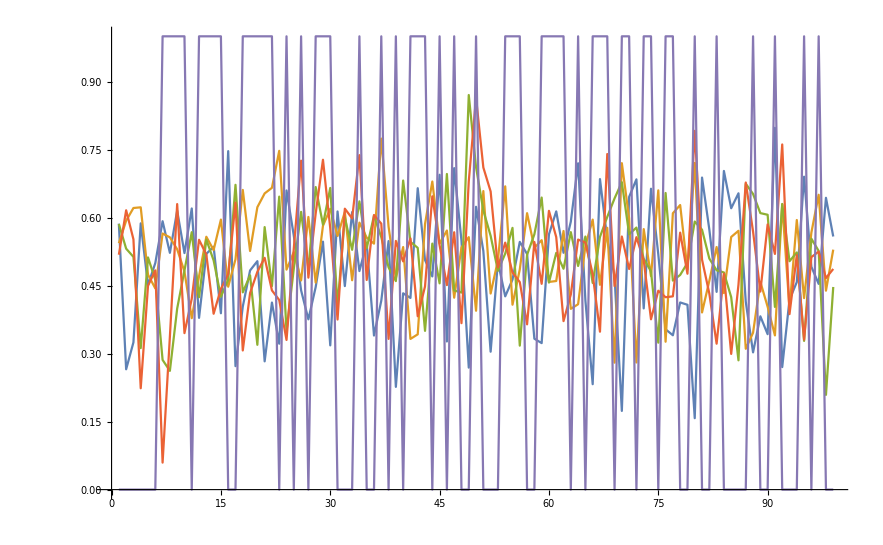

```mathematica
ListLinePlot@Table[Transpose[numeraiData[[1;;100]]][[i]][[2;;-1]],{i,50,54}]
```

### Extract correlations

```mathematica
Parallelize@Correlation[Table[Transpose[numeraiData[[1;;-1]]][[i]][[2;;-1]],{i,48,48}][[1]],Table[Transpose[numeraiData[[1;;-1]]][[i]][[2;;-1]],{i,54,54}][[1]]]
```

Parallelize::nopar1: Correlation[Table[Transpose[numeraiData⟦Span[«2»]⟧]⟦i⟧⟦2;;-1⟧,{i,48,48}]⟦1⟧,Table[Transpose[numeraiData⟦Span[«2»]⟧]⟦i⟧⟦2;;-1⟧,{i,54,54}]⟦1⟧] cannot be parallelized; proceeding with sequential evaluation.

-0.00205465

{{4,-0.0174076},{5,-0.0272479},{6,0.0082648},{7,0.00247683},{8,-0.0212572},{9,0.026584},{10,0.00437725},{11,0.0330428},{12,-0.00717062},{13,-0.0136491},{14,-0.0119827},{15,-0.00692132},{16,-0.00649706},{17,0.0379009},{18,0.0431967},{19,0.0244664},{20,-0.0449342},{21,0.0437895},{22,0.0429844},{23,-0.0151104},{24,0.00251977},{25,-0.00635699},{26,-0.00311609},{27,0.00823447},{28,0.0287507},{29,0.00337977},{30,-0.0206746},{31,0.03105},{32,0.0293325},{33,0.0456649},{34,0.0250361},{35,-0.0433865},{36,-0.0113329},{37,0.0149824},{38,0.0281955},{39,0.00365616},{40,-0.0122928},{41,0.00775423},{42,-0.0311166},{43,0.0276808},{44,0.0177164},{45,0.0157307},{46,0.00815523},{47,-0.00960186},{48,0.00322293},{49,0.00383797},{50,0.00785507},{51,-0.00923706},{52,0.0113908},{53,-0.0158421},{54,1}}

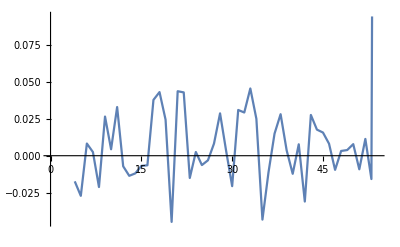

```mathematica
correlationTable=Table[{k,Correlation[Table[Transpose[numeraiData[[-10000;;-1]]][[i]][[2;;-1]],{i,k,k}][[1]],Table[Transpose[numeraiData[[-10000;;-1]]][[i]][[2;;-1]],{i,54,54}][[1]]]},{k,4,54}]
ListLinePlot@correlationTable
```

```mathematica
bestCorrelations=Reverse@Ordering[Abs@Transpose[correlationTable][[2]]][[-10;;-1]]
correlationTable[[bestCorrelations]]
bestCorrs=Transpose[correlationTable[[bestCorrelations]]][[1]]
```

{51,30,17,18,32,15,19,14,8,39}

{{54,1},{33,0.0456649},{20,-0.0449342},{21,0.0437895},{35,-0.0433865},{18,0.0431967},{22,0.0429844},{17,0.0379009},{11,0.0330428},{42,-0.0311166}}

{54,33,20,21,35,18,22,17,11,42}

```mathematica
correlMatrix=Table[Table[Correlation[Table[Transpose[numeraiData[[-1000;;-1]]][[i]][[2;;-1]],{i,k,k}][[1]],Table[Transpose[numeraiData[[-1000;;-1]]][[i]][[2;;-1]],{i,j,j}][[1]]],{k,4,54}],{j,4,54}];
```

```mathematica
correlMatrix//MatrixForm;
```

```mathematica
PrincipalComponents@correlMatrix//MatrixForm;
```

```mathematica
Correlation[Table[Transpose[numeraiData[[1;;-1]]][[i]][[-100000;;-1]],{i,33,33}][[1]],Table[Transpose[numeraiData[[1;;-1]]][[i]][[-100000;;-1]],{i,54,54}][[1]]]
```

-0.0203287

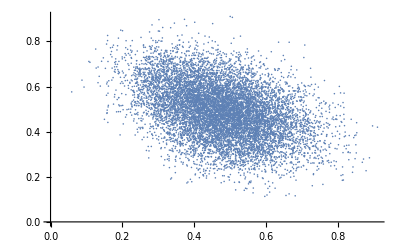

```mathematica
ListPlot[Transpose@{Table[Transpose[numeraiData[[1;;-1]]][[i]][[-10000;;-1]],{i,33,33}][[1]],Table[Transpose[numeraiData[[1;;-1]]][[i]][[-10000;;-1]],{i,20,20}][[1]]}]
```

```mathematica
(*Maximize correlation between feature and output.
Find a minimum set of features.
Minimum set of features should be maximally orthogonal.
*)
```

```mathematica
bestCorrs
```

{54,33,20,21,35,18,22,17,11,42}

```mathematica
topTen=Transpose[numeraiData[[-2000;;-1]]][[bestCorrs]];
topTenVal=Transpose[numeraiData[[-500;;-400]]][[bestCorrs]];
topTenTest=Transpose[numeraiData[[-4000;;-2000]]][[bestCorrs]];
```

```mathematica
Correlation[topTen[[1]],topTen[[6]]]
```

0.0702113

### Feature extraction - principal components

```mathematica
PrincipalComponents[Transpose[numeraiData[[-20;;-1]]][[4;;-1]]]//Dimensions
```

{51,20}

```mathematica
Table[Correlation[Transpose[numeraiData[[-120;;-1]]][[4;;-1]][[i]],Transpose[numeraiData[[-120;;-1]]][[4;;-1]][[-1]]],{i,1,51}]
```

{0.00394665,0.0716571,-0.113219,0.20967,0.00255826,0.051151,-0.0295273,0.261509,-0.124348,-0.190076,0.0694292,0.0801062,-0.0239956,0.194099,0.0248056,0.233137,-0.137173,0.147528,0.105779,0.0905734,0.165092,-0.100582,-0.026163,-0.0644271,0.173608,-0.0850009,-0.126268,-0.0757479,0.0733093,0.232313,0.162504,-0.246269,-0.0433423,0.0773043,0.125224,0.171854,-0.141894,0.0911568,0.0593108,0.167969,0.146121,0.0280908,0.055821,0.276822,-0.104196,0.00964948,-0.116374,0.0666126,0.187667,0.0199709,1}

```mathematica
4
```

4

```mathematica
PrincipalComponents[Correlation[Transpose[numeraiData[[-20;;-1]]][[4;;-1]]]]//MatrixForm;
```

### Model training

```mathematica
(*Training*)
trainInput=Transpose[topTen[[2;;-1]]];
trainOutput=topTen[[1]];
(*Validation*)
trainInputVal=Transpose[topTenVal[[2;;-1]]];
trainOutputVal=topTenVal[[1]];
(*Test*)
trainInputTest=Transpose[topTenTest[[2;;-1]]];
trainOutputTest=topTenTest[[1]];
```

```mathematica
f[arg_]:=arg[[1]]->arg[[2]]
trainSet=Table[f[{trainInput[[i]],trainOutput[[i]]}],{i,1,Length[trainInput]}];
trainSetTest=Table[f[{trainInputTest[[i]],trainOutputTest[[i]]}],{i,1,Length[trainInputTest]}];
(*trainSetVal=Table[f[{trainInputVal[[i]],trainOutputVal[[i]]}],{i,1,Length[trainInputVal]}];*)
```

```mathematica
(*methods={"LinearRegression","GaussianProcess","NearestNeighbors","NeuralNetwork","RandomForest"};*)
methods={"LinearRegression"};
```

```mathematica
Options[Predict]
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→None,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ValuePriors→Automatic}

```mathematica
(*ValidationSet->trainSetVal*)
(*PredictorMeasurements[net[[1]],{trainSet[[3]]},"LogLikelihood"]*)
```

```mathematica
nets=Parallelize@Table[Predict[trainSet,Method->methods[[i]],PerformanceGoal->"Quality"],{i,1,Length@methods}]//AbsoluteTiming;
StringJoin[{"Timing is: ",ToString@nets[[1]]," seconds"}]
net=nets[[2]];
```

Timing is: 2.2656 seconds

```mathematica
netTrainOutput=Table[ParallelTable[net[[j]][trainInput[[i]]],{i,1,Length@trainInput}],{j,1,Length@net}];

actualTrain=Table[{i,trainOutput[[i]]},{i,1,Length[trainInput]}];
netTrain=Table[Table[{i,netTrainOutput[[j]][[i]]},{i,1,Length[trainInput]}],{j,1,Length@net}];
```

```mathematica
netTrainOutputTest=Table[Table[net[[j]][trainInputTest[[i]]],{i,1,Length@trainInputTest}],{j,1,Length@net}];

actualTrainTest=Table[{i,trainOutputTest[[i]]},{i,1,Length[trainInputTest]}];
netTrainTest=Table[Table[{i,netTrainOutputTest[[j]][[i]]},{i,1,Length[trainInputTest]}],{j,1,Length@net}];
```

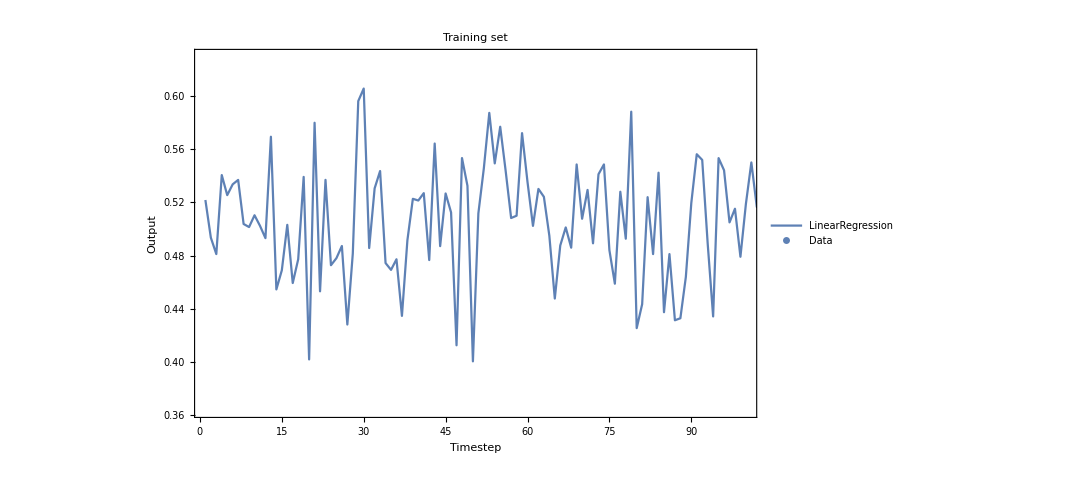

```mathematica
style[arg_]:=Table[Style[arg[[i]],16,Black],{i,1,Length@arg}]
plotOpts={PlotLegends->Placed[style[methods],{0.15,0.28}],Frame->True,FrameLabel->{Style["Timestep",18,Black],Style["Output",18,Black]},FrameStyle->Directive[Thickness[0.004],Black],ImageSize->800,FrameTicksStyle->18,PlotRange->{{1,100},Automatic}};Show[{ListLinePlot[netTrain,Evaluate@plotOpts,PlotLabel->Style["Training set",Black,18]],ListPlot[actualTrain,PlotLegends->Placed[{Style["Data",16,Black]},{0.45,0.85}]]}]
```

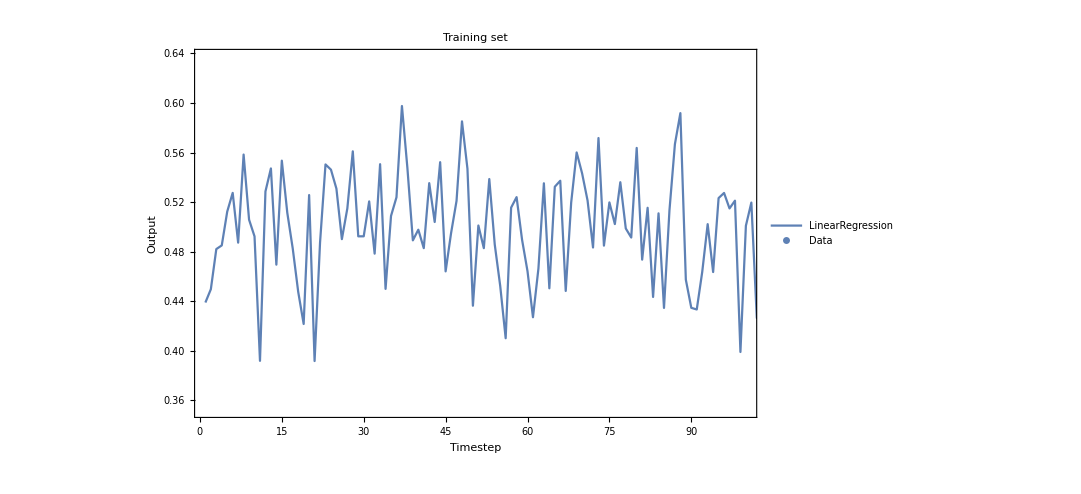

```mathematica
Show[{ListLinePlot[netTrainTest,Evaluate@plotOpts,PlotLabel->Style["Training set",Black,18]],ListPlot[actualTrainTest,PlotLegends->Placed[{Style["Data",16,Black]},{0.45,0.85}]]}]
```

```mathematica
(*Predicted and actual results on test data*)
trueResults=Transpose[actualTrainTest][[2]];
predictedResults=Transpose[netTrainTest[[1]]][[2]];
(*Compare first ten points for predicted and actual test data*)
trueResults[[1;;10]]
predictedResults[[1;;10]]
```

{1,0,1,0,1,1,1,1,1,0}

{0.438924,0.449674,0.482069,0.485028,0.512326,0.527406,0.487248,0.558359,0.505796,0.49234}

```mathematica
(*Define log loss function*)
logloss[binary_,prediction_]:=Table[-(binary[[i]]*Log[prediction[[i]]]+(1-binary[[i]])*Log[1-prediction[[i]]]),{i,1,Length@binary}]

(*Calculate the log loss for each time step, then find the mean*)
logloss=Mean@logloss[trueResults,predictedResults]
```

0.688043

```mathematica
loglossRolling[binary_,prediction_]:=Table[Table[-(binary[[i]]*Log[prediction[[i]]]+(1-binary[[i]])*Log[1-prediction[[i]]]),{i,1,j}],{j,1,Length@binary}]
AbsoluteTiming[Mean/@loglossRolling[trueResults,predictedResults]][[1]]
rollingLogLoss=Mean/@loglossRolling[trueResults,predictedResults];
```

11.7483

1471.78

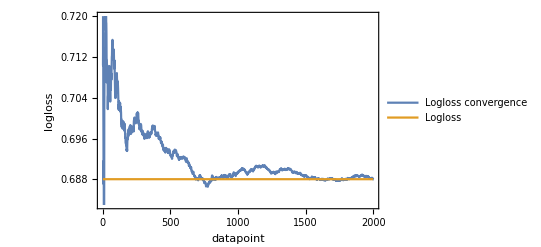

```mathematica
ListLinePlot[{rollingLogLoss,Table[logloss,2000]},PlotRange->{Automatic,{0.683,0.72}},PlotLegends->{"Logloss convergence","Logloss"},FrameLabel->{"datapoint","logloss"},Frame->True]
```

```mathematica
rollingLogLossSD=StandardDeviation/@loglossRolling[trueResults,predictedResults][[2;;-1]];
```

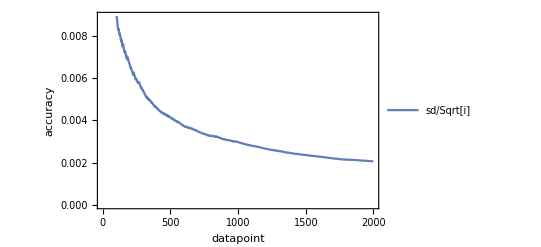

```mathematica
ListLinePlot[Table[rollingLogLossSD[[i]]/Sqrt[i],{i,1,Length@rollingLogLossSD-1}],PlotLegends->{"sd/Sqrt[i]"},FrameLabel->{"datapoint","accuracy"},Frame->True]
```

```mathematica
polar[f_]:=If[f>0.5,1,0]

polar2[f_]:=Table[If[f[[i]]>Mean[f],1,0],{i,1,Length@f}]
polarisedOutputTest=Table[polar/@netTrainOutputTest[[i]],{i,1,Length[net]}];
polarisedOutputTest2=Table[polar2@netTrainOutputTest[[i]],{i,1,Length[net]}];
```

```mathematica
tallys=Tally[{trainOutputTest-polarisedOutputTest[[1]]}[[1]]]
Log[Transpose[tallys][[2]][[2]]/Total@Transpose[tallys][[2]]//N]
```

{{1,438},{0,1087},{-1,476}}

-0.610225

```mathematica
Correlation[trainOutputTest,polarisedOutputTest[[1]]]
tallys=Tally[{trainOutputTest-polarisedOutputTest[[1]]}[[1]]]
Log[Transpose[tallys][[2]][[1]]/Total@Transpose[tallys][[2]]//N]
```

37 √(5/553007)

{{0,222},{1,75},{-1,104}}

-0.591284

```mathematica
Log[0.55]
```

-0.597837

```mathematica
0.08
```

```mathematica
Log@((0.04+1)/2)
```

-0.653926

```mathematica
Log[0.94]
```

-0.0618754

```mathematica
((0.086810+1)/2)
((0.086810+1)/2)
Log@((0.086810+1)/2)
```

0.543405

-0.6099

```mathematica
Table[{methods[[i]],Correlation[trainOutputTest,polarisedOutputTest[[i]]]//N},{i,1,5}]//N//TableForm
Table[{methods[[i]],Correlation[trainOutputTest,polarisedOutputTest2[[i]]]//N},{i,1,5}]//N//TableForm
```

LinearRegression | 0.0868102
GaussianProcess | -0.00391737
NearestNeighbors | 0.0308076
NeuralNetwork | 0.0811735
RandomForest | 0.0423775

LinearRegression | 0.0886948
GaussianProcess | -0.039719
NearestNeighbors | 0.0300731
NeuralNetwork | 0.0813274
RandomForest | 0.0383306

```mathematica
Table[{methods[[i]],Correlation[trainOutputTest,polarisedOutputTest[[i]]]//N},{i,1,5}]//N//TableForm
Table[{methods[[i]],Correlation[trainOutputTest,polarisedOutputTest2[[i]]]//N},{i,1,5}]//N//TableForm
```

LinearRegression | 0.111255
GaussianProcess | -0.0513116
NearestNeighbors | 0.034629
NeuralNetwork | 0.0315287
RandomForest | 0.0391697

LinearRegression | 0.111255
GaussianProcess | -0.00574083
NearestNeighbors | 0.0719402
NeuralNetwork | 0.0394656
RandomForest | 0.0404312

```mathematica
{trainOutputTest,polarisedOutputTest[[2]]}
```

{{1,1,0,0,0,1,1,1,1,0,1,1,0,0,1,1,0,1,1,0,1,0,1,1,1,1,1,0,0,1,1,0,1,0,0,0,1,0,1,1,0,0,1,0,0,0,0,1,1,0,0,1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,1,0,1,0,0,0,0,0,1,1,0,1,0,0,0,1,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
netTrainOutputTest[[1]]//Length
polarisedOutputTest[[1]]//Length
```

101

101

```mathematica
Table[{methods[[i]],Correlation[trainOutputTest,netTrainOutputTest[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.0237582
GaussianProcess | -0.0656737
NearestNeighbors | -0.156097
NeuralNetwork | -0.0414955
RandomForest | -0.0663517

```mathematica
Table[{methods[[i]],Correlation[trainOutputTest,netTrainOutputTest[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.0237582
GaussianProcess | -0.0656737
NearestNeighbors | -0.156097
NeuralNetwork | -0.0414955
RandomForest | -0.0663517

```mathematica
Table[{methods[[i]],Correlation[trainOutput,netTrainOutput[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.271168
GaussianProcess | 1.
NearestNeighbors | 0.39352
NeuralNetwork | 0.556203
RandomForest | 0.971899

```mathematica
Table[{methods[[i]],Correlation[trainOutput,netTrainOutput[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.250784
GaussianProcess | 1.
NearestNeighbors | 0.243345
NeuralNetwork | 0.283508
RandomForest | 0.977028

```mathematica
Table[{methods[[i]],Correlation[trainOutput,netTrainOutput[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.245425
GaussianProcess | 1.
NearestNeighbors | 0.39352
NeuralNetwork | 0.321731
RandomForest | 0.975278

```mathematica
Table[{methods[[i]],Correlation[trainOutput,netTrainOutput[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.271168
GaussianProcess | 1.
NearestNeighbors | 0.39352
NeuralNetwork | 0.556203
RandomForest | 0.972271

```mathematica
Table[{methods[[i]],Correlation[trainOutput,netTrainOutput[[i]]]},{i,1,5}]//TableForm
```

LinearRegression | 0.245425
GaussianProcess | 1.
NearestNeighbors | 0.39352
NeuralNetwork | 0.321731
RandomForest | 0.972532

```mathematica
actualTrain
```

{{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,0},{8,1},{9,0},{10,0},{11,1},{12,0},{13,1},{14,0},{15,0},{16,0},{17,0},{18,0},{19,1},{20,0},{21,1},{22,1},{23,1},{24,0},{25,0},{26,0},{27,1},{28,0},{29,1},{30,0},{31,1},{32,0},{33,1},{34,0},{35,0},{36,1},{37,0},{38,0},{39,1},{40,1},{41,0},{42,1},{43,1},{44,0},{45,1},{46,0},{47,0},{48,1},{49,0},{50,1},{51,1},{52,0},{53,0},{54,0},{55,1},{56,1},{57,1},{58,0},{59,0},{60,1},{61,0},{62,0},{63,0},{64,0},{65,1},{66,1},{67,1},{68,1},{69,0},{70,1},{71,1},{72,0},{73,0},{74,1},{75,1},{76,0},{77,0},{78,1},{79,0},{80,1},{81,1},{82,1},{83,0},{84,0},{85,1},{86,0},{87,0},{88,1},{89,1},{90,0},{91,0},{92,0},{93,0},{94,1},{95,0},{96,1},{97,1},{98,0},{99,1},{100,0},{101,0},{102,0},{103,0},{104,1},{105,1},{106,0},{107,0},{108,1},{109,1},{110,0},{111,0},{112,1},{113,1},{114,1},{115,0},{116,1},{117,0},{118,0},{119,1},{120,1},{121,0},{122,0},{123,1},{124,0},{125,1},{126,0},{127,1},{128,0},{129,0},{130,0},{131,1},{132,1},{133,0},{134,1},{135,0},{136,0},{137,0},{138,0},{139,1},{140,1},{141,1},{142,1},{143,0},{144,1},{145,0},{146,1},{147,0},{148,0},{149,0},{150,1},{151,0},{152,0},{153,0},{154,0},{155,1},{156,0},{157,0},{158,0},{159,1},{160,0},{161,1},{162,0},{163,0},{164,0},{165,0},{166,1},{167,0},{168,0},{169,1},{170,1},{171,0},{172,0},{173,0},{174,0},{175,0},{176,1},{177,0},{178,0},{179,0},{180,1},{181,1},{182,0},{183,0},{184,1},{185,1},{186,0},{187,0},{188,0},{189,1},{190,0},{191,1},{192,0},{193,0},{194,1},{195,0},{196,1},{197,0},{198,0},{199,1},{200,0}}

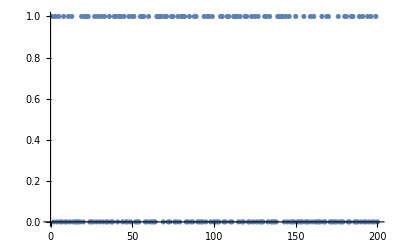

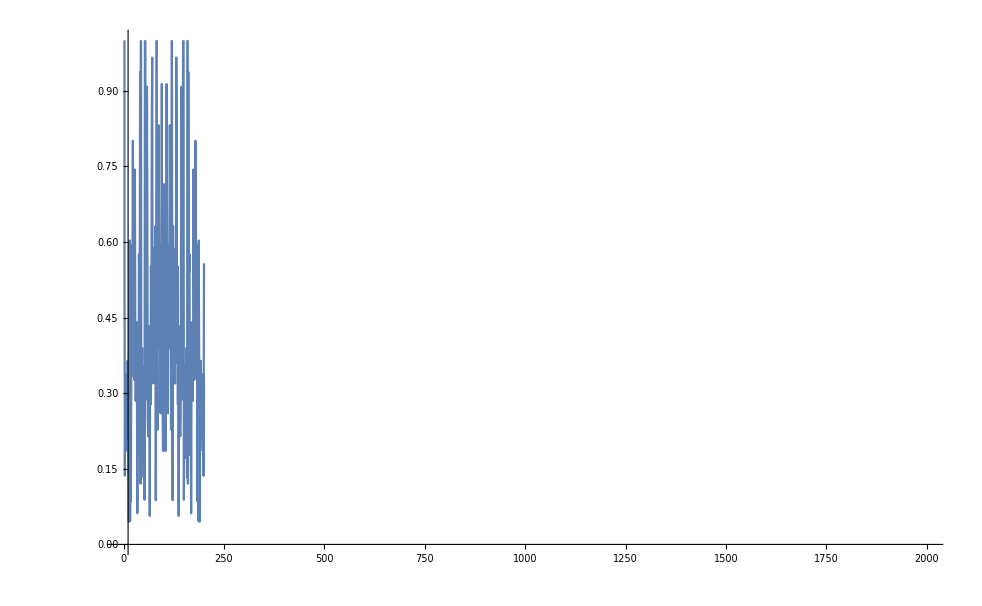

```mathematica
ListPlot@actualTrain
Abs@Fourier[Transpose[actualTrain][[2]]];
ListLinePlot[Abs@Fourier[Transpose[actualTrain][[2]]],PlotRange->{{1,2000},{0,1}}]
```